```mathematica
Get["/Users/austingottfredson/Documents/Macbook/School/20 Fall/Dark Matter/dlNdlxEW.m"]
```

-0.01

```mathematica
dlNdlxIEW["b"->"γ"][1000,Log[10,0.1]]
```

0.416798

#### Making Log Spaced Bins

Thanks to

```mathematica
Hyperlink[jVincent,"https://mathematica.stackexchange.com/questions/16324/is-there-a-mathematica-equivalent-to-matlabs-logspace"]
```

[jVincent](https://mathematica.stackexchange.com/questions/16324/is-there-a-mathematica-equivalent-to-matlabs-logspace)

```mathematica
fSpace[min_,max_,steps_,f_:Log]:=InverseFunction[ConditionalExpression[f[#],min<#<max]&]/@Range[f@min,f@max,(f@max-f@min)/(steps)]
```

```mathematica
bins=fSpace[0.5,1000,24]
```

{0.5,0.686298,0.942011,1.293,1.77477,2.43604,3.3437,4.58955,6.29961,8.64682,11.8686,16.2908,22.3607,30.6922,42.128,57.8247,79.3701,108.943,149.535,205.251,281.727,386.697,530.78,728.546,1000.}

I have the edges for 24 bins (25 values). I can access a bin boundary with:

```mathematica
Part[bins,1]
```

0.5

or just

```mathematica
bins[[1]]
```

0.5

#### Plotting

I want to plot the flux of photons from a DM DM annihilation in each energy bin as a function of the photon energy. That is ∫(dN/dE)ⅆE = ∫(dN/dlogx)/EⅆE

First, define a function for dN/dlogx (from PPPC 4 DM ID)

```mathematica
tophoton[mdm_,ephoton_]:=10^(dlNdlxIEW["b"->"γ"][mdm,Log[10,ephoton/mdm]])/ephoton
```

```mathematica
fluxinbin[bin_]:=NIntegrate[tophoton[1000,ephoton],{ephoton,bins[[bin]],bins[[bin+1]]}]
```

```mathematica
fluxinbin[1]
```

10.9602

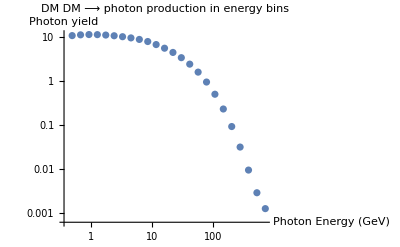

```mathematica
ListLogLogPlot[{{bins[[1]],fluxinbin[1]},{bins[[2]],fluxinbin[2]},{bins[[3]],fluxinbin[3]},{bins[[4]],fluxinbin[4]},{bins[[5]],fluxinbin[5]},{bins[[6]],fluxinbin[6]},{bins[[7]],fluxinbin[7]},{bins[[8]],fluxinbin[8]},{bins[[9]],fluxinbin[9]},{bins[[10]],fluxinbin[10]},{bins[[11]],fluxinbin[11]},{bins[[12]],fluxinbin[12]},{bins[[13]],fluxinbin[13]},{bins[[14]],fluxinbin[14]},{bins[[15]],fluxinbin[15]},{bins[[16]],fluxinbin[16]},{bins[[17]],fluxinbin[17]},{bins[[18]],fluxinbin[18]},{bins[[19]],fluxinbin[19]},{bins[[20]],fluxinbin[20]},{bins[[21]],fluxinbin[21]},{bins[[22]],fluxinbin[22]},{bins[[23]],fluxinbin[23]},{bins[[24]],fluxinbin[24]}},PlotLabel->"DM DM ⟶ photon production in energy bins",AxesLabel->{"Photon Energy (GeV)","Photon yield"}]
```

I tried other ways to make plotting this easier without success, thus I did it the long way.

```mathematica
data={}
```

{}

```mathematica
For[i=1,i<25,i++,Append[data,{fluxinbin[i],i}]]
```

```mathematica
data
```

{}

```mathematica
BinByBin={{bins[[1]],fluxinbin[1]},{bins[[2]],fluxinbin[2]},{bins[[3]],fluxinbin[3]},{bins[[4]],fluxinbin[4]},{bins[[5]],fluxinbin[5]},{bins[[6]],fluxinbin[6]},{bins[[7]],fluxinbin[7]},{bins[[8]],fluxinbin[8]},{bins[[9]],fluxinbin[9]},{bins[[10]],fluxinbin[10]},{bins[[11]],fluxinbin[11]},{bins[[12]],fluxinbin[12]},{bins[[13]],fluxinbin[13]},{bins[[14]],fluxinbin[14]},{bins[[15]],fluxinbin[15]},{bins[[16]],fluxinbin[16]},{bins[[17]],fluxinbin[17]},{bins[[18]],fluxinbin[18]},{bins[[19]],fluxinbin[19]},{bins[[20]],fluxinbin[20]},{bins[[21]],fluxinbin[21]},{bins[[22]],fluxinbin[22]},{bins[[23]],fluxinbin[23]},{bins[[24]],fluxinbin[24]}}
```

{{0.5,10.9602},{0.686298,11.4062},{0.942011,11.5856},{1.293,11.5346},{1.77477,11.2843},{2.43604,10.8763},{3.3437,10.3468},{4.58955,9.71289},{6.29961,8.9656},{8.64682,8.03105},{11.8686,6.84704},{16.2908,5.65445},{22.3607,4.52707},{30.6922,3.4384},{42.128,2.44858},{57.8247,1.61043},{79.3701,0.956701},{108.943,0.504224},{149.535,0.232242},{205.251,0.0924275},{281.727,0.0314601},{386.697,0.00939388},{530.78,0.0028565},{728.546,0.00124004}}

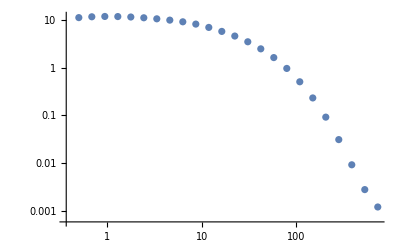

```mathematica
ListLogLogPlot[BinByBin]
```

#### Now add J factor

I suppose I can just multiply the observed J factor from a specific line of sight dwarf spheroidal galaxy.

Bootes I: J -> 18.8

```mathematica
JBootes=18.8;
```

```mathematica
BootesBinByBin = BinByBin[[All,2]] * JBootes
```

{206.052,214.437,217.81,216.85,212.144,204.474,194.519,182.602,168.553,150.984,128.724,106.304,85.1089,64.6419,46.0332,30.2761,17.986,9.4794,4.36615,1.73764,0.59145,0.176605,0.0537022,0.0233128}

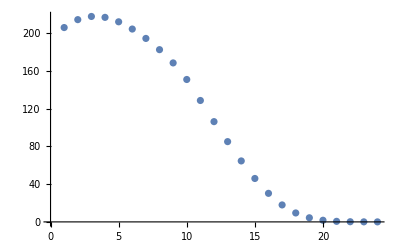

```mathematica
ListPlot[BootesBinByBin]
```

```mathematica
Export["specfile.txt",BinByBin]
```

specfile.txt

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["specfile.txt"]]]
```

```mathematica
bins[[25]]
```

1000.